```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
(*Расширяющаяся труба - задача для внутреннего течения*)
(*pts={{6.3,0},{6.3,0.6},{-0.2,0.6},{-0.5,0.3},{-3.5,0.3},{-3.5,0},{-3.5,-0.3},{-0.5,-0.3},{-0.2,-0.6},{6.3,-0.6},{6.3,0}};
h=π/400.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента А.Н.Нуриева*)
delta=10^-4;
pts={{0.05+delta,0.0},{0.05+delta,0.5+delta},{-0.05-delta,0.5+delta},{-0.05-delta,0.0},{-0.05-delta,-0.5-delta},{0.05+delta,-0.5-delta},{0.05+delta,0.0}};
h=(0.1+2 delta)/20.;
```

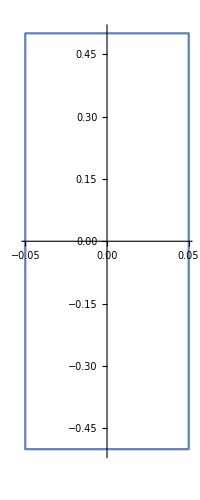

```mathematica
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
vertex=Flatten[Table[SplitLine[pts[[i]],pts[[i+1]],h,LastPoint->False],{i,Length@pts-1}],1];
```

```mathematica
ListPlot[vertex,AspectRatio->Automatic]
```

-Graphics-

```mathematica
n=Length@vertex
```

440

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["pointsVP",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: pointsVP"<>StringRepeat[" ",57]<>"|
| Info: Points for velocity and pressure computation (rect01Nuriev440)"<>"(n="<>ToString[Length[vertex]]<>")"<>StringRepeat[" ",6-StringLength["n="<>ToString[Length[vertex]]]]<>"|
\*---------------------------------------------------------------------------*/"
}
~Join~{"history = {"}
~Join~
Table[{"{",vertex[[i,1]],",",vertex[[i,2]],"},"},{i,n-1}]
~Join~
{{"{",vertex[[-1,1]],",",vertex[[-1,2]],"}"}}
,"Table"]
```

pointsVP